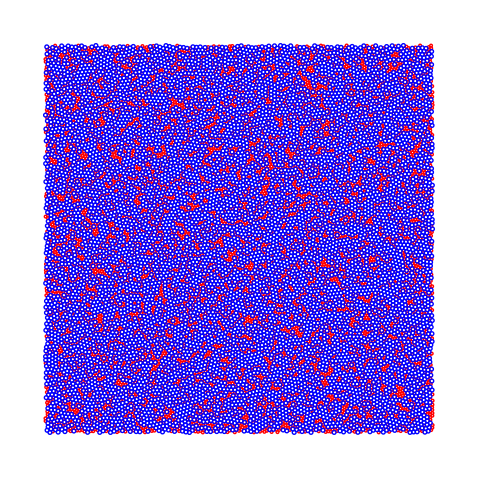

```mathematica
ClearAll[file,fp,gp];
file=Import["G:\\jamming\\cudajamming\\positionsecond.txt","Table"];
A=file[[1]];
F=Circle[{#[[1]],#[[2]]},#[[3]]]&;
graph=Graphics[Style[F[#1],If[#1[[3]]>0.6,Blue,Red]]]&;
Show[graph/@file]
```

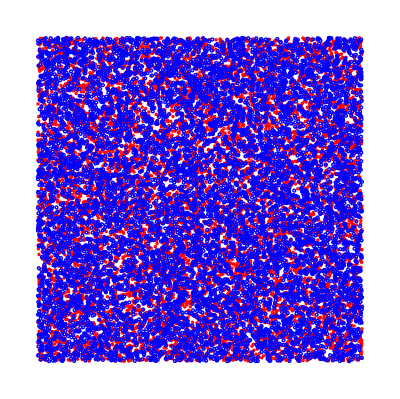

```mathematica
ClearAll[file,fp,gp];
file=Import["C:\\Users\\zhangjiahao\\Desktop\\jamming\\cudajamming\\positionfirst.txt","Table"];
A=file[[1]];
F=Circle[{#[[1]],#[[2]]},#[[3]]]&;
graph=Graphics[Style[F[#1],If[#1[[3]]>0.6,Blue,Red]]]&;
Show[graph/@file]
```